```mathematica
h=25
```

25

```mathematica
V=3
```

3

```mathematica
FindRoot[{h*((1/2)Log[(Cos[bs/2]+Sin[bs/2])/(Cos[bs/2]-Sin[bs/2])]-(1/2)Log[(Cos[be/2]+Sin[be/2])/(Cos[be/2]-Sin[be/2])]+(1/(Cos[be]) - 1/Cos[bs])*(Sin[bs]/Cos[bs]))==-8,h*((1/(Cos[bs]) - 1/Cos[be]))==0},{{bs,-0.5},{be,0.3}}, Method->"Secant"]
```

{bs→-0.314674,be→0.314674}

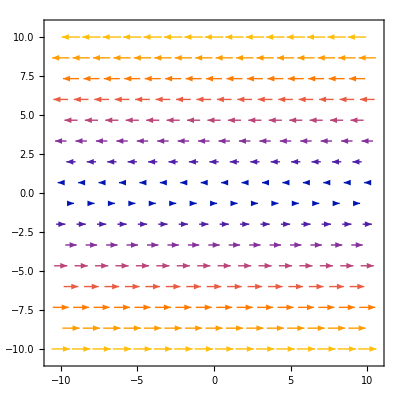

```mathematica
VectorPlot[{-(V/h)*y,0},{x,-10,10},{y,-10,10},VectorScaling->Automatic,VectorSizes->Automatic]
```

```mathematica
eqs={x'[t]==V*Cos[b[t]]-(V/h)*y[t],
y'[t]==V*Sin[b[t]],
b'[t]==(V/h)*(Cos[b[t]])^2}
```

{x'[t]==3 Cos[b[t]]-(3 y[t])/25,y'[t]==3 Sin[b[t]],b'[t]==3/25 Cos[b[t]]^2}

```mathematica
sol=NDSolve[Join[eqs,{x[0]==-8,y[0]==0,b[0]==-0.3146744480632316}],{x[t],y[t],b[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],b[t]→InterpolatingFunction[…][t]}}

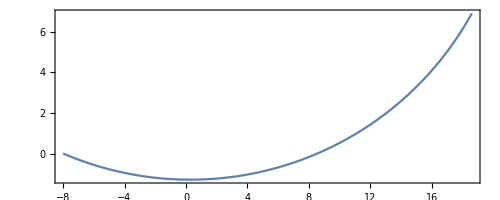

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,10},Frame->True]
```